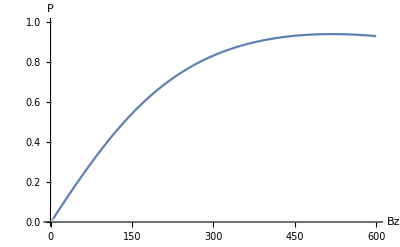

```mathematica
Q=-4.945;Cp=-40;Cv=-23;De=1420;gammae=2.802;gamman=-0.003;(*Subscript[T, 1]=1;Subscript[T, 20]=33;Subscript[T, 21]=1;*)
Subscript[Γ, 0]=0.1;Subscript[Γ, 1]=2;Subscript[T, 11]=0.001;Subscript[T, 12]=0.00001;Subscript[T, 21]=33;Subscript[T, 22]=0.001;theta=0.00;psi=0*π/180;
He={{Cp+De+Bz gamman+Q+Bz gammae Cos[psi],0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0,0,0},{0,De+Bz gammae Cos[psi],0,Cv,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0,0},{0,0,-Cp+De-Bz gamman+Q+Bz gammae Cos[psi],0,Cv,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0},{gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Cv,0,Bz gamman+Q,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0},{0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Cv,0,0,0,Cv,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0},{0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,-Bz gamman+Q,0,Cv,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2))},{0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Cv,0,-Cp+De+Bz gamman+Q-Bz gammae Cos[psi],0,0},{0,0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Cv,0,De-Bz gammae Cos[psi],0},{0,0,0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,Cp+De-Bz gamman+Q-Bz gammae Cos[psi]}};
H=He;
(*H[[7,7]]=E1;*)Rho=Array[rho,{9,9}];Sigma=Table[0,{90},{9},{9}];K=Table[0,{90},{9},{9}];sum=1;For[i=1,i≤9,i++,For[j=1,j≤9,j++,Sigma[[sum++]][[i,j]]=1;]]
For[i=1,i≤9,i++,K[[i]][[i,i]]=1;]
(*1-6: spontaneous decay, spin-conversing, 7-12:excited states-singlet, 13-18: singlet-ground states*, 19-24: optical excitation*)
L=ConstantArray[0,{9,9}];
For[i=1,i≤3,i++,For[j=1,j≤3,j++,If[j-i≠0,L=L+Subscript[T, 11]/2*(2*Sigma[[i*9-9+j]].Rho.Transpose[Sigma[[i*9-9+j]]]-Transpose[Sigma[[i*9-9+j]]].Sigma[[i*9-9+j]].Rho-Rho.Transpose[Sigma[[i*9-9+j]]].Sigma[[i*9-9+j]]),Continue]]]
For[i=4,i≤6,i++,For[j=4,j≤6,j++,If[j-i≠0,L=L+Subscript[T, 11]/2*(2*Sigma[[i*9-9+j]].Rho.Transpose[Sigma[[i*9-9+j]]]-Transpose[Sigma[[i*9-9+j]]].Sigma[[i*9-9+j]].Rho-Rho.Transpose[Sigma[[i*9-9+j]]].Sigma[[i*9-9+j]]),Continue]]]
For[i=7,i≤9,i++,For[j=7,j≤9,j++,If[j-i≠0,L=L+Subscript[T, 11]/2*(2*Sigma[[i*9-9+j]].Rho.Transpose[Sigma[[i*9-9+j]]]-Transpose[Sigma[[i*9-9+j]]].Sigma[[i*9-9+j]].Rho-Rho.Transpose[Sigma[[i*9-9+j]]].Sigma[[i*9-9+j]]),Continue]]]
For[i=1,i≤9,i++,For[j=1,j≤9,j++,If[j-i==3,L=L+Subscript[T, 11]/2*(2*Sigma[[i*9-9+j]].Rho.Transpose[Sigma[[i*9-9+j]]]-Transpose[Sigma[[i*9-9+j]]].Sigma[[i*9-9+j]].Rho-Rho.Transpose[Sigma[[i*9-9+j]]].Sigma[[i*9-9+j]]),Continue]]]
For[i=1,i≤3,i++,For[j=1,j≤3,j++,If[j-i≠0,L=L+Subscript[T, 22]/2*(2*(K[[i]]-K[[j]]).Rho.(K[[i]]-K[[j]])-(K[[i]]-K[[j]]).(K[[i]]-K[[j]]).Rho-Rho.(K[[i]]-K[[j]]).(K[[i]]-K[[j]])),Continue]]]
For[i=4,i≤4,i++,For[j=4,j≤6,j++,If[j-i≠0,L=L+Subscript[T, 22]/2*(2*(K[[i]]-K[[j]]).Rho.(K[[i]]-K[[j]])-(K[[i]]-K[[j]]).(K[[i]]-K[[j]]).Rho-Rho.(K[[i]]-K[[j]]).(K[[i]]-K[[j]])),Continue]]]
For[i=7,i≤9,i++,For[j=7,j≤9,j++,If[j-i≠0,L=L+Subscript[T, 22]/2*(2*(K[[i]]-K[[j]]).Rho.(K[[i]]-K[[j]])-(K[[i]]-K[[j]]).(K[[i]]-K[[j]]).Rho-Rho.(K[[i]]-K[[j]]).(K[[i]]-K[[j]])),Continue]]]
For[i=1,i≤9,i++,For[j=1,j≤9,j++,If[j-i==3,L=L+Subscript[T, 21]/2*(2*(K[[i]]-K[[j]]).Rho.(K[[i]]-K[[j]])-(K[[i]]-K[[j]]).(K[[i]]-K[[j]]).Rho-Rho.(K[[i]]-K[[j]]).(K[[i]]-K[[j]])),Continue]]]
For[i=4,i≤6,i++,L=L+Subscript[Γ, 0]/2*(2*Sigma[[(i-4)*9+i]].Rho.Transpose[Sigma[[(i-4)*9+i]]]-Transpose[Sigma[[(i-4)*9+i]]].Sigma[[(i-4)*9+i]].Rho-Rho.Transpose[Sigma[[(i-4)*9+i]]].Sigma[[(i-4)*9+i]])]
For[i=4,i≤6,i++,L=L+Subscript[Γ, 0]/2*(2*Sigma[[(i+2)*9+i]].Rho.Transpose[Sigma[[(i+2)*9+i]]]-Transpose[Sigma[[(i+2)*9+i]]].Sigma[[(i+2)*9+i]].Rho-Rho.Transpose[Sigma[[(i+2)*9+i]]].Sigma[[(i+2)*9+i]])]
For[i=1,i≤3,i++,L=L+Subscript[Γ, 1]/2*(2*Sigma[[(i+2)*9+i]].Rho.Transpose[Sigma[[(i+2)*9+i]]]-Transpose[Sigma[[(i+2)*9+i]]].Sigma[[(i+2)*9+i]].Rho-Rho.Transpose[Sigma[[(i+2)*9+i]]].Sigma[[(i+2)*9+i]])]
For[i=7,i≤9,i++,L=L+Subscript[Γ, 1]/2*(2*Sigma[[(i-4)*9+i]].Rho.Transpose[Sigma[[(i-4)*9+i]]]-Transpose[Sigma[[(i-4)*9+i]]].Sigma[[(i-4)*9+i]].Rho-Rho.Transpose[Sigma[[(i-4)*9+i]]].Sigma[[(i-4)*9+i]])]
M=-ⅈ*(H.Rho-Rho.H)+L;M[[9,9]]=Rho[[1,1]]+Rho[[2,2]]+Rho[[3,3]]+Rho[[4,4]]+Rho[[5,5]]+Rho[[6,6]]+Rho[[7,7]]+Rho[[8,8]]+Rho[[9,9]]-1;F[Bz_]:=((Rho[[4,4]]-Rho[[6,6]])/(Rho[[4,4]]+Rho[[5,5]]+Rho[[6,6]]))/.Solve[Flatten[M==ConstantArray[0,{9,9}]],Flatten[Rho]][[1]];Plot[F[Bz],{Bz,0,600},PlotRange->{0,1},AxesLabel->{Bz,P}, AxesOrigin->{0,0}]
```